# Blinding Energy from Liquid Drop model

```mathematica
BE[A_,n_,z_]:=-a1 A + a2 A^(2/3)+a3 z^2/A^(1/3)+a4 (n-z)^2/A-Which[ Mod[n,2]==0 && Mod[z,2]==0,1, Mod[n,2]==1 &&  Mod[z,2]==1,-1, Mod[n+z,2]==1,0] a5 A^((- 3)/4)
```

```mathematica
a1=15.6;
a2=16.8;
a3=0.72;
a4=23.3;
a5=34;
```

```mathematica
(* BE lower, more stable, and BE > 0 unstable. BE = Q *)
(* s = 1 for even (n & z ), s= -1 for odd (n & z ), s= 0 for others*)
```

```mathematica
K=Table[BE[n+z,n,z]/(n+z),{z,1,200},{n,1,200}];
```

```mathematica
ListContourPlot[K,Contours->Range[-10,0,1],ContourLabels->All]
```

-Graphics-

```mathematica
ISOBAR[n_,Minz_,Maxz_]:=Table[BE[n+z,n,z]/(n+z),{z,Minz,Maxz,1}]
ISOTOP[z_,Minn_,Maxn_]:=Table[{n+z,BE[n+z,n,z]/(n+z)},{n,Minn,Maxn,1}]
ISOAZ[A_,Minz_,Maxz_]:=Table[BE[A,A-z,z]/(A),{z,Minz,Maxz,1}]
ISOAN[A_]:=Table[BE[A,n,A-n]/(A),{n,1,A-1,1}]
```

```mathematica
ListPlot[{ISOTOP[8,6,16]},Joined->True,Mesh->All,AxesLabel->{ "A", "B.E./A"}]
```

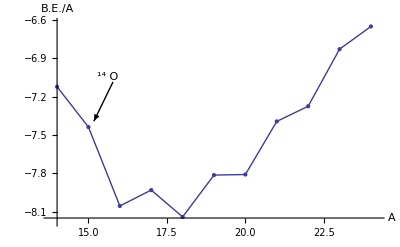

```mathematica
ISOTOP[8,6,16]//TableForm
```

14 | -7.12384
15 | -7.43874
16 | -8.05561
17 | -7.93149
18 | -8.14127
19 | -7.81433
20 | -7.80978
21 | -7.39447
22 | -7.27594
23 | -6.82984
24 | -6.6519

```mathematica
ListPlot[{ISOAZ[22,7,12]},Joined->True,Mesh->All,AxesLabel->{ "Z", "B.E."}]
```

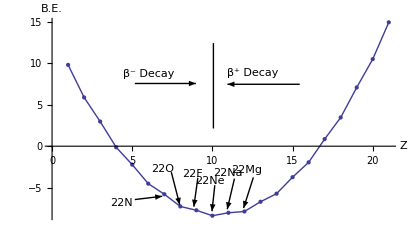

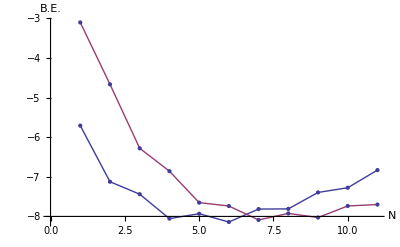

```mathematica
ListPlot[{ISOTOP[8,5,15],ISOTOP[9,4,14]},Joined->True,Mesh->All, AxesLabel->{ "N", "B.E."}]
```